```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
activeLEC=Import["./PlotLECs.dat","Table"];
lambdas=activeLEC[[All,1]];
```

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+lam^2))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{locall=lam},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
widths={};
rndPrec=5;
Do[
widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];
widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];
AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[2 λ^0.5,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[((eigsorted[[1]]<results)&&(eigsorted[[1]]>-2.5)&&(Im[eigsorted[[1]]]==0)),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];

DiagDimer[lamd_,wSet_]:=Block[{LECc,e0,λ=lamd,wi=wSet},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Nd=Length[wi];
hamm=Table[ham[2 λ^0.5,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
e0=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
{e0,optSet}
];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^2/(4 (core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];

VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2= (8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2));
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2));
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(4 (1./4) lam^2+2 Bb-2 Hh)+Aa (-4 (1/4) lam^2-2 Bb+2 Hh))/(2 (2 (1/4) lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

Do[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=ParallelTable[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints},ProgressReporting->False]; 

AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins"];
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

```mathematica
(* Plot parameters for the visualization of V(r,r') *)
nR=100;rMi=0.01;rMa=2.5;
hdiff=(rMa-rMi)/nR;
rR=Range[rMi,rMa,hdiff];
nR=Length[rR];

energ=0.001;
nref=Max[{IntegerPart[Length[lambdas]/2.],1}];

(* dimer wave-function parameter *)
dimDimer=4;nparallelThreads=8;nDimerWidthSamples=100000;minDimerWidth=0.1;maxDimerWidth=3.5 lambdas[[nref]];midWidthdiff=0.1;

plotdatadimerWFKT={};pltLabs={};
useOneReferenceDimerBasis=True;
If[useOneReferenceDimerBasis==True,{e0ref,dimerref}=ApproxDimerWF[lambdas[[nref]],dimDimer,nparallelThreads,nDimerWidthSamples,minDimerWidth,maxDimerWidth,midWidthdiff,0];];

Do[
maxDimerWidth=2 lambdaTest;
If[useOneReferenceDimerBasis==False,
{e0Core,dimerCore}=DiagDimer[lambdaTest,dimerref[[All,2]]],
{e0Core,dimerCore}=ApproxDimerWF[lambdaTest,dimDimer,nparallelThreads,nDimerWidthSamples,minDimerWidth,maxDimerWidth,midWidthdiff,0]];

AppendTo[pltLabs,e0Core];
JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@dimerCore];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

AppendTo[plotdatadimerWFKT,Transpose[{rR,JacobiTrailWavefunctionDataU}]];

normCore=1/NormTF[dimerCore];
dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Grid[{{"EFT parameters","plot control"},{"cutoff regulator λ = "<>ToString[lambdaTest],"#(plot grid points) = "<>ToString[nR]},{"C_0(λ) = "<>ToString[LECc]},{"B(2) = "<>ToString[e0Core],"dimer-basis dimension = "<>ToString[dimCore]}},Frame->All];

potnoloc3d={};potloc={};
Do[
cij=-hdiff^3 mh2 dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]]  normCore;

potloctmp=ParallelTable[{i hdiff,-cij/hdiff VlocTF[i hdiff,2 lambdaTest^0.5,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]]]},{i,1,Length[rR]}];
AppendTo[potloc,potloctmp];

potnoloc3dtmp=
Flatten[ParallelTable[{i hdiff,j hdiff,cij WnolocTF3[i hdiff,j hdiff,energ,2 lambdaTest^0.5,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],0,mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];
AppendTo[potnoloc3d,potnoloc3dtmp]

,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}];

potloc=Transpose[{potloc[[1]][[All,1]],Total[potloc[[All,All,2]]]}];
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];

Put[potloc,"locPot_"<>ToString[lambdaTest]<>".dat"];
Put[potnonloc3d,"nonlocPot_"<>ToString[lambdaTest]<>".dat"];
Print["λ=",lambdaTest,": E_0^(dimer)=",e0Core]
,{lambdaTest,lambdas}];
```

λ=4.: E_0^(dimer)=-1.73912

λ=8.: E_0^(dimer)=-1.60334

λ=12.: E_0^(dimer)=-1.51295

λ=16.: E_0^(dimer)=-1.47586

λ=20.: E_0^(dimer)=-1.3469

λ=24.: E_0^(dimer)=-1.19426

λ=28.: E_0^(dimer)=-1.14951

λ=32.: E_0^(dimer)=-1.1511

λ=36.: E_0^(dimer)=-0.951588

λ=40.: E_0^(dimer)=-0.802913

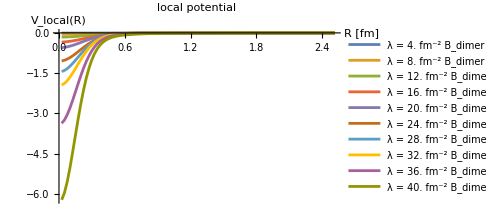
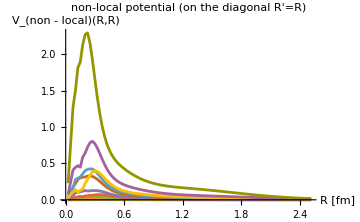
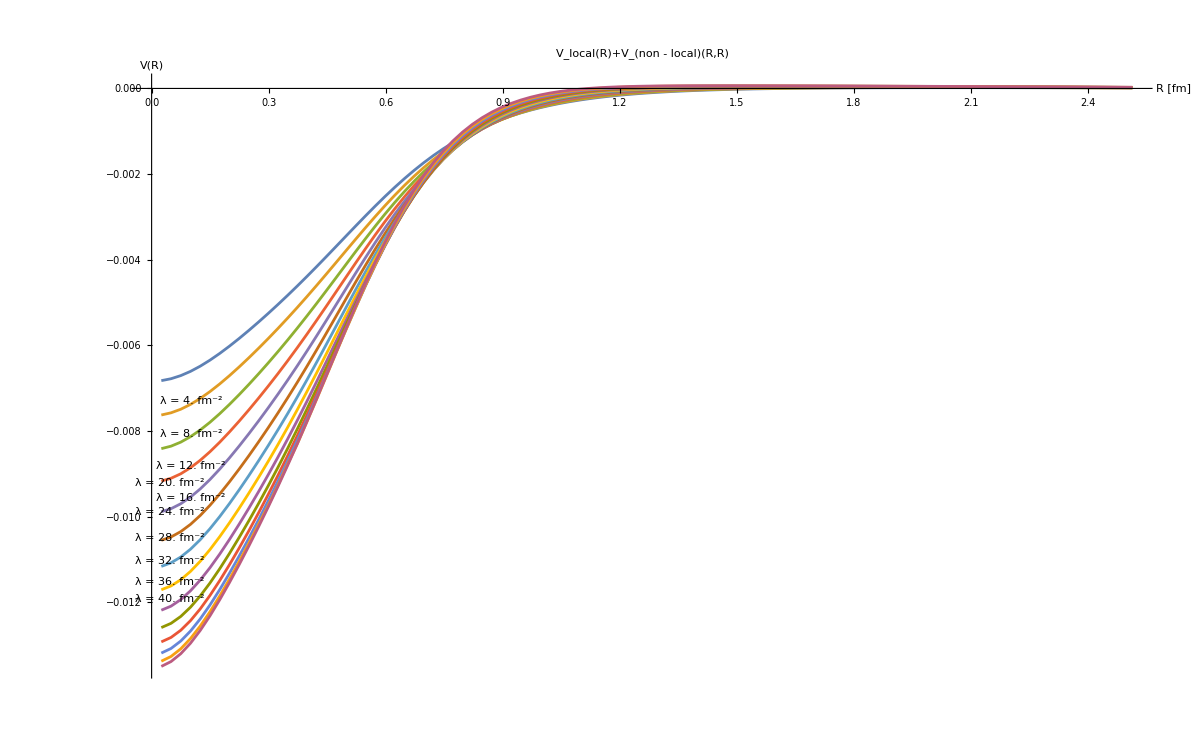
-Graphics- | -Graphics-
-Graphics- |

```mathematica
dataloc=Get["locPot_"<>ToString[#]<>".dat"]&/@lambdas;
datanonloc=Get["nonlocPot_"<>ToString[#]<>".dat"]&/@lambdas;

datanonlocdiagtmp=Select[#,#[[1]]==#[[2]]&]&/@datanonloc;
datanonlocdiag=datanonlocdiagtmp[[All,All,{1,3}]];

plotdatloc=dataloc[[#]]&/@Range[Length[lambdas]];
plotdatnloc=datanonlocdiag[[#]]&/@Range[Length[lambdas]];
pltdatSum=Transpose[{plotdat[[1]][[All,1]],#}]&/@plotdat[[All,All,2]]+plotdat2[[All,All,2]];

pltdat=Join[plotdatloc,plotdatnloc,pltdatSum];

Grid[{{ListPlot[plotdatloc,PlotRange->Full,Joined->True,AxesLabel->{"R [fm]","V_local(R)"},PlotLegends->{"λ = "<>ToString[#[[1]]]<>" fm^-2   B_dimer = "<>ToString[#[[2]]]<>" MeV"&/@Transpose[{lambdas,pltLabs}]},ImageSize->Medium,PlotLabel->"local potential"],ListPlot[plotdatnloc,PlotRange->Full,Joined->True,AxesLabel->{"R [fm]","V_(non - local)(R,R)"},ImageSize->Medium,PlotLabel->"non-local potential (on the diagonal R'=R)"]},{ListPlot[pltdatSum,PlotRange->Full,Joined->True,AxesLabel->{"R [fm]","V(R)"},ImageSize->{1200,2400},PlotLabel->"V_local(R)+V_(non - local)(R,R)",PlotLabels->Placed["λ = "<>ToString[#]<>" fm^-2"&/@lambdas,Left]]}}]
```

```mathematica
lambdasshow=lambdas;
data=Get["nonlocPot_"<>ToString[#]<>".dat"]&/@lambdasshow;
vid=Animate[ListPlot3D[Re[data[[n]]],PlotRange->All],{n,Range[1,Length[lambdasshow],1]}]
```

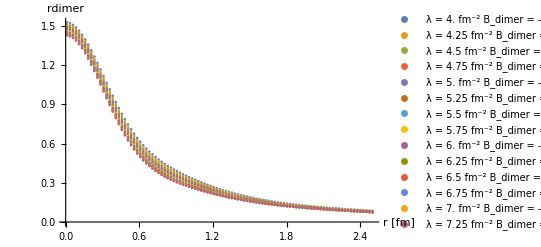

```mathematica
ListPlot[#&/@plotdatadimerWFKT,PlotRange->Full,AxesLabel->{"r [fm]","rdimer"},PlotLegends->{"λ = "<>ToString[#[[1]]]<>" fm^-2   B_dimer = "<>ToString[#[[2]]]<>" MeV"&/@Transpose[{lambdas,pltLabs}]}]
```

```mathematica
Export["test.avi",vid]
```

test.avi